# Warehouse Data

## Database Construction

Baoxiang Pan

```mathematica
data=Import["/Users/lambda/Documents/Code/Emma/Warehouse/cp2.txt","Table",CharacterEncoding -> "UTF8"];
```

```mathematica
Dimensions[data]
```

{34745,1}

```mathematica
Rdata=ArrayReshape[data,{34745/5,5}];
```

```mathematica
Dimensions[Rdata]
```

{6949,5}

```mathematica
R2data=DeleteDuplicatesBy[Rdata,#[[3]]&];
```

```mathematica
Dimensions[R2data]
```

{4719,5}

```mathematica
TableForm[R2data[[1;;100]]]
```

（出租）大兴京开高【丙2类】【智能分拣库】70000㎡招租 | 大兴 生物医药基地  | 大兴地铁天宫院附近或或生物医药基地 | 70000㎡ | 1.3元/㎡/天  
（出租）45-340平南五环高立庄库房精装修可办公仓库 | 大兴 兴丰大街  | 黄村镇周村工业区附近或念坛公园西门 | 200㎡ | 0.8元/㎡/天  
（出租）大鲁店物流沅10000平米高台库出租 | 朝阳 豆各庄  | 大鲁店物流园附近或通马路、京津高速 | 10000㎡ | 面议  
（出租）西三期库房出租.厂房仓储物流一体 | 海淀 西三旗  | 京藏高速附近或南口 | 600.0㎡ | 0.5元/㎡/天  
（出租）北清路温泉1800平米可做生产、办公、库房 | 海淀 西北旺  | 北清路附近或白家疃 | 1800㎡ | 1.5元/㎡/天  
（出租）西五环外衙门口库房.厂房500-12000平米出租 | 石景山 衙门口  | 西五环衙门口桥西附近或融景城 | 2000㎡ | 1.3元/㎡/天  
（出租）四季青桥东公园库房300㎡可以分组 | 海淀 四季青  | 西四环附近或四季青桥 | 300㎡ | 2元/㎡/天  
（出租）来广营比目鱼2000平大开间可做【独立大门头】 | 朝阳 来广营  | 方恒国际浦项中心华彩大厦附近或朝来科技园新华科技大厦 | 2000㎡ | 2.4元/㎡/天  
（出租）北五环附近4万平米物流厂房库房加工 | 昌平 南口  | 小汤山附近或北五环外 | 40000.0㎡ | 1.0元/㎡/天  
（出租）东三环地下室双井劲松可做各类工作室轰趴等 | 朝阳 劲松  | 华腾园小区附近或劲松桥 | 860.0㎡ | 0.7元/㎡/天  
（出租）望京独栋800平独栋办公出租 | 朝阳 望京  | 望京附近或望京 | 800㎡ | 4元/㎡/天  
（出租）西直门【腾达大厦】新出260㎡精装不要错过 | 西城 西直门  | 西直门外大街168号附近或凯旋大厦 | 260㎡ | 7.5元/㎡/天  
（出租）个人昌平沙河厂房库房出租紧邻京新京藏高速 | 昌平 沙河  | 昌平区沙河镇附近或G6G7高速 | 4000.0㎡ | 72000.0元/月  
（出租）【嘉汇伟业】石景山衙门口800㎡、可注册、各行各业 | 石景山 衙门口  | 衙门口南街15号院附近或五环桥边上 | 800㎡ | 1.5元/㎡/天  
（出租）新国展仓库后沙峪仓库文件存储红酒仓库自助仓 | 顺义 新国展  | 天竺附近或机场后沙峪新国展 | 100.0㎡ | 1.0元/㎡/天  
（出租）【地铁边上的5A写字楼】开发商直租 | 朝阳 垡头  | 7号线百子湾欢乐谷附近或焦奥中心 | 930㎡ | 4元/㎡/天  
（出租）衙门口大开间10000㎡大库房挑高10米随意分割 | 石景山 衙门口  | 石景山附近或衙门口 | 10000㎡ | 1.3元/㎡/天  
（出租）【丙二类消防】5000平米高台库+10000平米 | 大兴 黄村  | 北京市大兴区天河北路附近或六环路京开高速 | 5000㎡ | 面议  
（出租）临机场高速独栋独立人口草场地艺术区530平看房方便 | 朝阳 酒仙桥  | 悠乐汇草场地798艺术区附近或望京SOHO麒麟社星源 | 530㎡ | 2.8元/㎡/天  
（出租）中关村上地北专业仓储全托管物流快递配送一体化 | 海淀 中关村  | 中关村附近或上地 | 4200.0㎡ | 0.5元/㎡/天  
（出租）3000平仓库低价出租 | 朝阳 来广营  | 立水桥地铁站口附近或古玩城旁边 | 3000㎡ | 面议  
（出租）物业出租自然新天地4000平仓库可分租 | 丰台 马家堡  | 南三环草桥洋桥中间附近或首地大峡谷附近 | 4000㎡ | 2元/㎡/天  
（出租）大兴长子营平库3毛5可以分租 | 大兴 大兴周边  | 马朱路附近或长子营工业区 | 5000㎡ | 0.35元/㎡/天  
（出租）上地小营西路【45平办公室可做库房】特价出租 | 海淀 上地  | 上地附近或二炮南门 | 45㎡ | 1.3元/㎡/天  
（出租）西二旗京包路高台库1600平出租 | 海淀 西二旗  | 西二旗附近或京包路 | 1600㎡ | 1元/㎡/天  
（出租）房山窦店标准仓库平整货场独立办公区(个人) | 房山 房山周边  | 房山区窦店镇附近或窦店环岛 | 2500㎡ | 面议  
（出租）海淀区小规模、一般纳税人注册地址第二年半价优惠出租 | 海淀 中关村  | 绿创大厦、富海大厦、附近或寰岛博雅 | 20㎡ | 1580元/月  
（出租）望京500平精装独栋办公出租 | 朝阳 望京  | 望京附近或花家地 | 500㎡ | 4.7元/㎡/天  
（出租）【嘉汇伟业】保鲜库房1300㎡【可分租】随时看房 | 石景山 鲁谷  | 五里坨附近或五里坨 | 1300㎡ | 2.5元/㎡/天  
（出租）金源对面超值高大尚仓库冷库办公摄影体育项目 | 海淀 世纪城  | 海淀区板井路附近或车道沟地铁西侧 | 2000㎡ | 2.5元/㎡/天  
（出租）新华科技大厦1770平【送1000平露台】可分租 | 朝阳 酒仙桥  | 华彩大厦诚盈中心方恒国际附近或浦项中心嘉美中心新港大厦 | 1770㎡ | 4元/㎡/天  
（出租）顺义天北路独院租赁影视文化体育等主题园区1.6元 | 顺义 机场  | 天北路附近或天竺 | 17000.0㎡ | 1.6元/㎡/天  
（出租）北清路庄辛桥库房出租 | 昌平 沙河  | 北清路附近或幸庄桥 | 1360㎡ | 面议  
（出租）石景山层高8米可分租可办公可仓库无业态限制 | 石景山 玉泉路  | 衙门口附近 | 2000㎡ | 1.3元/㎡/天  
（出租）南三环丰台玉泉营桥万兴大厦高挑高400—900㎡ | 丰台 玉泉营  | 南三环附近或玉泉营桥 | 500㎡ | 4.2元/㎡/天  
（出租）装修家具长短期存放生活用品存储恒温恒湿地上仓库 | 朝阳 CBD  | 顺义天竺镇府前街4号附近或天竺、新国展、机场后沙峪 | 18㎡ | 面议  
（出租）东风5号【500平遗留装修】3.8元免费停车 | 朝阳 酒仙桥  | 颐堤港新港大厦兆维大厦附近或绿地中心浦项中心诚盈中心 | 500㎡ | 3.8元/㎡/天  
（出租）新华科技大厦850平精装带办公家具包物业供＊ | 朝阳 望京  | 京物大厦宏源大厦牡丹集团附近或叶青大厦中轻大厦博雅国际 | 850㎡ | 4.5元/㎡/天  
（出租）临时存放家具、公司办公用品、字画、档案存储5折 | 海淀 玉泉路  | 顺义天竺府前街4号附近或天竺、新国展、机场后沙峪 | 20㎡ | 面议  
（出租）南中轴路8万平米仓库库房平库高台库 | 大兴 大兴周边  | 大兴区魏善庄镇西沙窝村附近或庞各庄 | 80000㎡ | 面议  
（出租）个人昌平沙河G6G7高速附近仓库出租 | 昌平 沙河  | 沙河镇老牛湾附近或G6G7高速 | 5000㎡ | 0.6元/㎡/天  
（出租）1至50平米小仓库出租按天计费安东自助仓储 | 海淀 五道口  | 海淀区牡丹园地铁B口附近附近或牡丹园马甸五道口 | 20㎡ | 面议  
（出租）寰岛博雅【海淀办公室出租】【可注册可迁址办公】 | 海淀 公主坟  | 环岛博雅大厦绿创大厦附近或万寿路地铁站 | 20㎡ | 1580元/月  
（出租）四季青紫竹院路板井路远大路各种面积出租库房 | 海淀 世纪城  | 海淀四季青附近或世纪金源附近 | 4000㎡ | 2.0元/㎡/天  
（出租）西五环衙门口标准库房600到6000平高8米可注册 | 海淀 四季青  | 西五环衙门口附近 | 6000㎡ | 1.3元/㎡/天  
（出租）骏一孵化器直租【43平米适合6-8人】仓库出租 | 海淀 上地  | 上地附近或安宁庄 | 43㎡ | 1.2元/㎡/天  
（出租）个人出租厂房库房紧邻京藏京新高速 | 昌平 沙河  | 昌平沙河镇附近或紧邻G6G7高速 | 4500.0㎡ | 81000.0元/月  
（出租）北京小面办公室注册公司变更地址一般纳税人行政秘书 | 朝阳 国贸  | 朝阳门东直门北新桥东单王附近或三元桥呼家楼国贸十里堡东 | 18㎡ | 2000元/月  
（出租）通州潞城厂库房1700平 | 通州 潞城  | 六环附近或通燕高速 | 1700㎡ | 面议  
（出租）88-101平米电商仓库专业代管非中介; | 朝阳 酒仙桥  | 东五环内七棵树桥出口附附近或朝阳大悦城姚家园路青年路 | 101㎡ | 面议  
（出租）通州台湖镇工业园厂房个人出租价格面谈面积大小都有 | 通州 梨园  | 台湖工业园区附近 | 1000㎡ | 面议  
（出租）上地东路2500平库房出租 | 海淀 上地  | 上地附近或五街 | 2500㎡ | 1元/㎡/天  
（出租）四季青桥西巨山路500平库房可做冷库和办公 | 海淀 四季青  | 西四环四季青桥西杏石口路附近或杏石口桥翰林学院 | 500㎡ | 1.4元/㎡/天  
（出租）大兴南中轴路4000平高台库出租(可托管) | 大兴 大兴周边  | 南六环附近或南中轴路 | 4000㎡ | 面议  
（出租）闵庄路1500平米汽修办公区唯一面积在租 | 海淀 香山  | 闵庄路附近或西山森林公园 | 1500㎡ | 2元/㎡/天  
（出租）物品存储按天计费1至100立方小库房出租 | 朝阳 三里屯  | 酒仙桥北路1号院附近或798望京花家地 | 20.0㎡ | 3.3元/㎡/天  
（出租）新华科技251平精装落地窗免费摆渡车到地铁14号线 | 朝阳 酒仙桥  | 京物大厦宏源大厦牡丹集团附近或恒通国际商务园北广集团 | 251㎡ | 面议  
（出租）1马驹桥六号桥1000平米高台库对外出租 | 大兴 亦庄  | 马驹桥六号桥附近或马驹桥物流园 | 1000㎡ | 0.95元/㎡/天  
（出租）国有工业用地可定制高台库房 | 海淀 上地  | 上庄水库附近或上庄小学 | 3500㎡ | 0.4元/㎡/天  
（出租）【可分租】宋庄东六环徐辛庄出口9000平米库房出租 | 通州 宋庄  | 东六环附近 | 9000㎡ | 220000元/月  
（出租）出租地下空间淘宝店库房办公室 | 朝阳 石佛营  | 十里堡附近或爱这城小区 | 2000.0㎡ | 1.5元/㎡/天  
（出租）库房出租价格优惠交通便利 | 海淀 海淀周边  | 五环边附近 | 1000㎡ | 1.5元/㎡/天  
（出租）国有工业园标准库房出租 | 昌平 霍营  | 北清路附近或生命科学园 | 2200㎡ | 面议  
（出租）四季青桥西15000平200平起分餐饮考虑 | 海淀 四季青  | 四季青西附近或中间建筑 | 300㎡ | 3.5元/㎡/天  
（出租）通州马驹桥标准高台库2500平9毛随时入住 | 通州 马驹桥  | 东南六环6号桥附近或马大路 | 2500㎡ | 面议  
（出租）马驹桥40000平高台库房低价出租 | 通州 马驹桥  | 南六环附近或马驹桥6号桥东南物流 | 40000㎡ | 0.8元/㎡/天  
（出租）花园桥车道沟地铁仓库办公出租350/500/280 | 海淀 世纪城  | 花园桥西车道沟地铁西北角附近或世纪城 | 500㎡ | 3.5元/㎡/天  
（出租）五环外2万平仓库100平起租可分租可托管 | 朝阳 建外大街  | 金盏电商物流园内附近或金盏电商物流园内 | 20000㎡ | 面议  
（出租）20000平米仓库火爆出租西北旺西三旗上地仓储 | 海淀 西北旺  | 昌平附近或城北 | 20000.0㎡ | 0.5元/㎡/天  
（出租）通州厂库房1000平独门独院 | 通州 张家湾  | 103国道附近或六环 | 1000㎡ | 面议  
（出租）【精装带家具5元】500平诚盈中心地下一层直通地铁 | 朝阳 来广营  | 颐堤港新港大厦兆维大厦附近或朝来科技园新华科技大厦 | 500㎡ | 5元/㎡/天  
（出租）小仓库、装修家具、生活用品存储、医疗器械、公司货物 | 海淀 中关村  | 顺义天竺镇府前街4号附近或新国展、后沙峪、天竺 | 20㎡ | 面议  
（出租）大兴【独门独院高台库】85000㎡出租1元 | 大兴 大兴周边  | 大兴附近或京开高速附近 | 80000㎡ | 1元/㎡/天  
（出租）朝阳区小红门乡博大路库房 | 朝阳 小红门  | 朝阳区小红门乡博大路东侧附近 | 3000㎡ | 1元/㎡/天  
（出租）宋庄小堡画室出租 | 通州 宋庄  | 宋庄附近或小堡 | 2400㎡ | 0.8元/㎡/天  
（出租）【厂库房办公住宿】宋庄2200平厂房出租 | 通州 宋庄  | 宋梁路附近或燕通高速 | 2200㎡ | 面议  
（出租）白石桥东紧邻地铁交通方便整层1200㎡低价出租 | 海淀 白石桥  | 海淀区白石桥东附近或方圆大厦 | 1200㎡ | 6元/㎡/天  
（出租）个人昌平沙河京藏京新高速附近仓库出租 | 大兴 黄村  | 福田汽车厂旁附近或沙阳路 | 5000.0㎡ | 90000.0元/月  
（出租）黄金地段自然新天地4000平库房甩租随意分割 | 丰台 木樨园  | 马家堡东路106号附近或永辉超市楼上 | 4000㎡ | 2元/㎡/天  
（出租）亦庄独栋写字楼整租2万平米 | 大兴 亦庄  | 亦庄附近或京东大厦 | 20000㎡ | 2元/㎡/天  
（出租）海淀适合学校15000平带教学楼操场食堂宿舍 | 海淀 北洼路  | 上庄附近或京新高速 | 15000.0㎡ | 1.0元/㎡/天  
（出租）新建独门院高台库12000平场地充足大车可随意掉头 | 大兴 大兴周边  | 北臧村附近或魏永路京开高速六环 | 13000.0㎡ | 13200.0元/㎡/天  
（出租）顺义中央别墅区商业旺铺3000平米可分租连锁品牌 | 顺义 中央别墅区  | 地铁附近 | 3000㎡ | 面议  
（出租）带院库房1500平办公、住宿、放货均可 | 石景山 鲁谷  | 西五环莲石路附近附近或衙门口纸库 | 1500㎡ | 1元/㎡/天  
（出租）【200平米】独门独院可进大车 | 通州 宋庄  | 徐尹路附近或东六环 | 200㎡ | 面议  
（出租）朝阳区五方桥附近仓库出租 | 朝阳 豆各庄  | 朝阳区万子营附近 | 3000㎡ | 面议  
（出租）绿创环保集团【教育培训】可注册可分割【企业办公】 | 昌平 立水桥  | 昌平县城龙泽南口北七家附近或昌平城区振兴路28号 | 168㎡ | 2元/㎡/天  
（出租）上地后厂村路1500平库房出租 | 海淀 上地  | 上地附近或后厂村 | 1500㎡ | 0.7元/㎡/天  
（出租）望京地铁14号线【天启大厦】700平包物业供＊ | 朝阳 望京  | 众运大厦洛娃大厦福码大厦附近或叶青大厦中轻大厦博雅国际 | 700㎡ | 4.8元/㎡/天  
（出租）张家湾厂房一万平米出租 | 通州 张家湾  | 张家湾附近或张家湾政府附近 | 10000㎡ | 1.5元/㎡/天  
（出租）物品存储按天计费1-100立方小库房出租 | 朝阳 左家庄  | 安贞华联附近或798望京花家地 | 30㎡ | 面议  
（出租）超大类仓储现对外招租交通方便大车进出方便 | 昌平 阳坊  | 北六环阳坊附近或昌平阳坊 | 50000.0㎡ | 0.5元/㎡/天  
（出租）出租北京小仓库 | 朝阳 燕莎  | 东三环北路6号汇佳大厦附近或外交大厦 | 200㎡ | 面议  
（出租）双桥水郡长安楼房一层带花园库房出租 | 朝阳 双桥  | 水郡长安家园附近或双桥地铁站 | 154.0㎡ | 6500.0元/月  
（出租）1至30平小仓库出租1天起租优立仓自助仓储 | 朝阳 燕莎  | 东三环北路6号汇佳大厦附近或亮马桥地铁B口出 | 30㎡ | 面议  
（出租）【4元起地铁边上的写字楼】焦奥中心开发商直租 | 朝阳 垡头  | 7号线百子湾化工路附近或焦奥中心 | 4800㎡ | 4元/㎡/天  
（出租）马家堡4000地下仓库出租中 | 丰台 洋桥  | 洋桥南马家堡东106号附近或10号地铁角门东 | 4000㎡ | 2元/㎡/天  
（出租）磁各庄中轴路高13米仓库招租1800平米价钱面议 | 大兴 亦庄  | 亦庄南附近或磁各庄 | 1800㎡ | 面议  
（出租）仓库出租、公司货物存储、电商中转库房按天计算 | 昌平 立水桥  | 顺义天竺府前街4号附近或天竺、新国展、机场 | 20㎡ | 面议  
（出租）附近地铁14号线【酒仙桥东路】3300平米整层 | 朝阳 酒仙桥  | 酒仙桥北路789艺术区附近或兆维大厦恒通商务园 | 3300㎡ | 4元/㎡/天

GeoPlot

#### Import Data

```mathematica
SetDirectory["/Users/lambda/Documents/Code/Emma/Warehouse/"];
bj=Block[{data},
	data=Import["0208tidybj.xlsx"];
	data=data[[1,2;;,;;]];
	data=Select[data,And[#[[6]]>114,#[[5]]>39.4,#[[5]]<43,#[[6]]<118]&];
	Map[{{#[[5]],#[[6]]},#[[7]],#[[8]]}&,data]];
tj=Block[{data},
	data=Import["0216tidytj.xlsx"];
	data=data[[1,2;;,;;]];
	data=Select[data,And[#[[8]]>112,#[[7]]>35,#[[7]]<43]&];
	Map[{{#[[7]],#[[8]]},#[[9]],#[[10]]}&,data]];
hb=Block[{data},
	data=Import["0219tidyhb.xlsx"];
	data=data[[1,2;;,;;]];
	data=Map[{{#[[8]],ToExpression[#[[9]]]},#[[10]],#[[11]]}&,data];
	Select[data,And[#[[1,1]]>35,#[[1,1]]<43,#[[1,2]]>112]&]];
```

```mathematica
data=Join[bj,tj,hb];
Dimensions[data]
```

{7216,3}

#### Plot

```mathematica
PointColorGeoPlot[data_,bounds_]:=Module[{position,area,price,colorf,plotLegend,legend,graph,d},
	(*dataform: {{lat,lon},area,price} *)
	d=Select[data,And[#[[1,1]]>bounds[[1,1]],#[[1,1]]<bounds[[1,2]],#[[1,2]]>bounds[[2,1]],#[[1,2]]<bounds[[2,2]]]&];
	position=Map[#[[1]]&,d];
	area=Map[#[[2]]&,d];
	price=Map[#[[3]]&,d];
    colorf=Blend[{{0, Red}, {4, Green}}, #]&;
	plotLegend[{min_, max_}, n_, col_] := 
      Graphics[MapIndexed[{{col[#1], Rectangle[{0, #2[[1]] - 1}, {1, #2[[1]]}]}, 
                           {Black, 
                            Text[NumberForm[N@#1, {4, 2}], {4, #2[[1]] - .5}, {1, 0}]}} &, 
                            Rescale[Range[n], {1, n}, {min, max}]],
						    Frame -> False, FrameTicks -> None, PlotRangePadding -> 1.2];
    legend=Labeled[plotLegend[{0,4},13,colorf],"price",Top];
	graph=GeoGraphics[Table[{PointSize[If[area[[i]]<100,0.0025,
											If[area[[i]]<1000,0.005,
												If[area[[i]]<10000,0.01,0.02]]]],
									   colorf[price[[i]]],
									   Point[Reverse[position[[i]]]]},{i,Length[price]}],
					  GeoRange->bounds];
	Grid[{{Show[graph, ImageSize -> {Automatic, 600}], 
           Show[legend, ImageSize -> {Automatic, 300}]}}]];
```

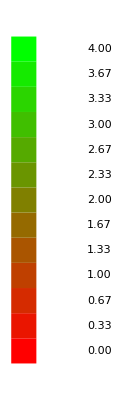
-Graphics- | -Graphics-priceDistribution Of Warehouses in JingJinJi Area

-Graphics- | -Graphics-priceDistribution Of Warehouses in JingJinJi Area

-Graphics- | -Graphics-priceDistribution Of Warehouses in JingJinJi Area

```mathematica
wholePlot=PointColorGeoPlot[data,{{36,42},{113,122.5}}];
Labeled[wholePlot,"Distribution Of Warehouses in JingJinJi Area",Top]
```

```mathematica
wholePlot=PointColorGeoPlot[hb,{{36,42},{113,122.5}}];
Labeled[wholePlot,"Distribution Of Warehouses in Hebei Province",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Hebei Province

```mathematica
bjPlot=PointColorGeoPlot[bj,{{39.4,40.5},{115.8,117.4}}];
Labeled[bjPlot,"Distribution Of Warehouses in Beijing",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Beijing

```mathematica
tjPlot=PointColorGeoPlot[tj,{{38.72,39.6},{116.8,117.8}}];
Labeled[tjPlot,"Distribution Of Warehouses in Tianjin",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Tianjin

```mathematica
sjzPlot=PointColorGeoPlot[hb,{{37.8,38.3},{114.25,114.85}}];
Labeled[sjzPlot,"Distribution Of Warehouses in Shijiazhuang",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Shijiazhuang

```mathematica
tsPlot=PointColorGeoPlot[hb,{{39.5,39.8},{117.9,118.5}}];
Labeled[tsPlot,"Distribution Of Warehouses in Tangshan",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Tangshan

```mathematica
test[data_,bounds_]:=Module[{position,area,price,colorf,plotLegend,legend,graph,d},
	(*dataform: {{lat,lon},area,price} *)
	d=Select[data,And[#[[1,1]]>bounds[[1,1]],#[[1,1]]<bounds[[1,2]],#[[1,2]]>bounds[[2,1]],#[[1,2]]<bounds[[2,2]]]&];
	position=Map[#[[1]]&,d];
	area=Map[#[[2]]&,d];
	price=Map[#[[3]]&,d];
    colorf=Blend[{{0, Red}, {4, Green}}, #]&;
	plotLegend[{min_, max_}, n_, col_] := 
      Graphics[MapIndexed[{{col[#1], Rectangle[{0, #2[[1]] - 1}, {1, #2[[1]]}]}, 
                           {Black, 
                            Text[NumberForm[N@#1, {4, 2}], {4, #2[[1]] - .5}, {1, 0}]}} &, 
                            Rescale[Range[n], {1, n}, {min, max}]],
						    Frame -> False, FrameTicks -> None, PlotRangePadding -> 1.2];
    legend=Labeled[plotLegend[{0,4},13,colorf],"price",Top];
	graph=GeoGraphics[Table[{PointSize[If[area[[i]]<100,0.0025,
											If[area[[i]]<1000,0.005,
												If[area[[i]]<10000,0.01,0.02]]]],
									   colorf[price[[i]]],
									   Point[Reverse[position[[i]]]]},{i,Length[price]}],
					  GeoRange->bounds,
					  GeoBackground->None];
	graph]
```

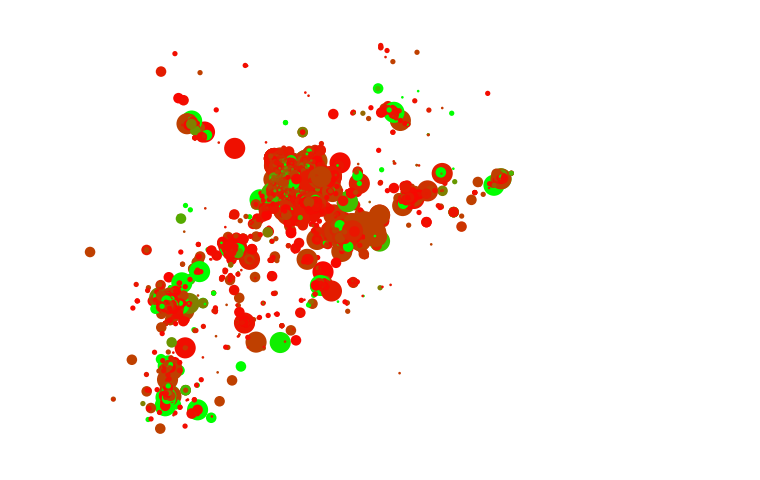

```mathematica
testPlot=test[data,{{36,42},{113,122.5}}]
```

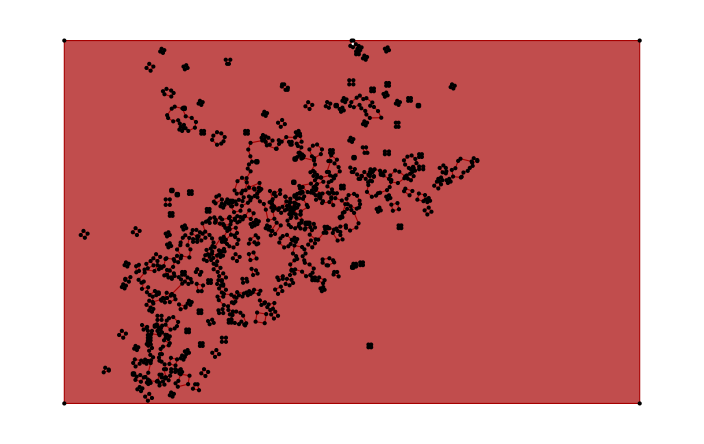

```mathematica
ImageMesh[testPlot]
```

```mathematica
wholePlot=PointColorGeoPlot[hb,{{36.3,37.1},{114.1,114.965}}];
Labeled[wholePlot,"Distribution Of Warehouses in Xingtai Handan",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Xingtai Handan

```mathematica
wholePlot=PointColorGeoPlot[hb,{{38.65,39.1},{115.25,115.67}}];
Labeled[wholePlot,"Distribution Of Warehouses in Baoding",Top]
```

-Graphics- | -Graphics-priceDistribution Of Warehouses in Baoding